```mathematica
FindFormulaPath[g_]:=Block[{},
Monitor[
formulaDepth=0;FindFormulaPath[g,Table[{v},{v,VertexList[g]}]],
formulaDepth
]
]
```

```mathematica
FindFormulaPath[g_,v_]:=Block[{edge,pos1,pos2,v2,result={},added,contracted},
If[CompleteGraphQ[g],
result={}
,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
added=EdgeAdd[g,edge];
contracted=VertexContract[g,{edge[[1]],edge[[2]]}];
result=Join[
{{VertexCount[g],EdgeCount[g]}->{VertexCount[added],EdgeCount[added]},
{VertexCount[g],EdgeCount[g]}->{VertexCount[contracted],EdgeCount[contracted]}},
FindFormulaPath[added,v],
FindFormulaPath[contracted,v2]
]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

```mathematica
Length[ListofVars[FindFullFormula[MinimalGraph2[8]]]]
```

203

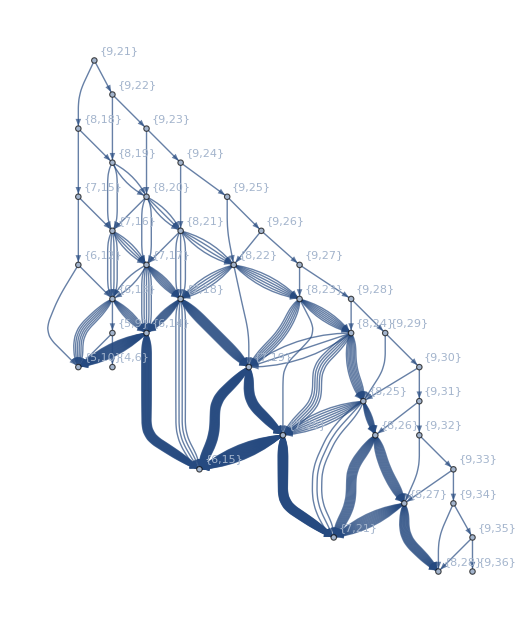

```mathematica
gg=Graph[FindFormulaPath[MinimalGraph[8]],VertexLabels->"Name"]
```

```mathematica
Table[v->VertexInDegree[gg,v],{v,Select[VertexList[gg],VertexOutDegree[gg,#]==0&]}]
```

{{8,28}→15,{9,36}→1,{7,21}→65,{6,15}→90,{5,10}→31,{4,6}→1}

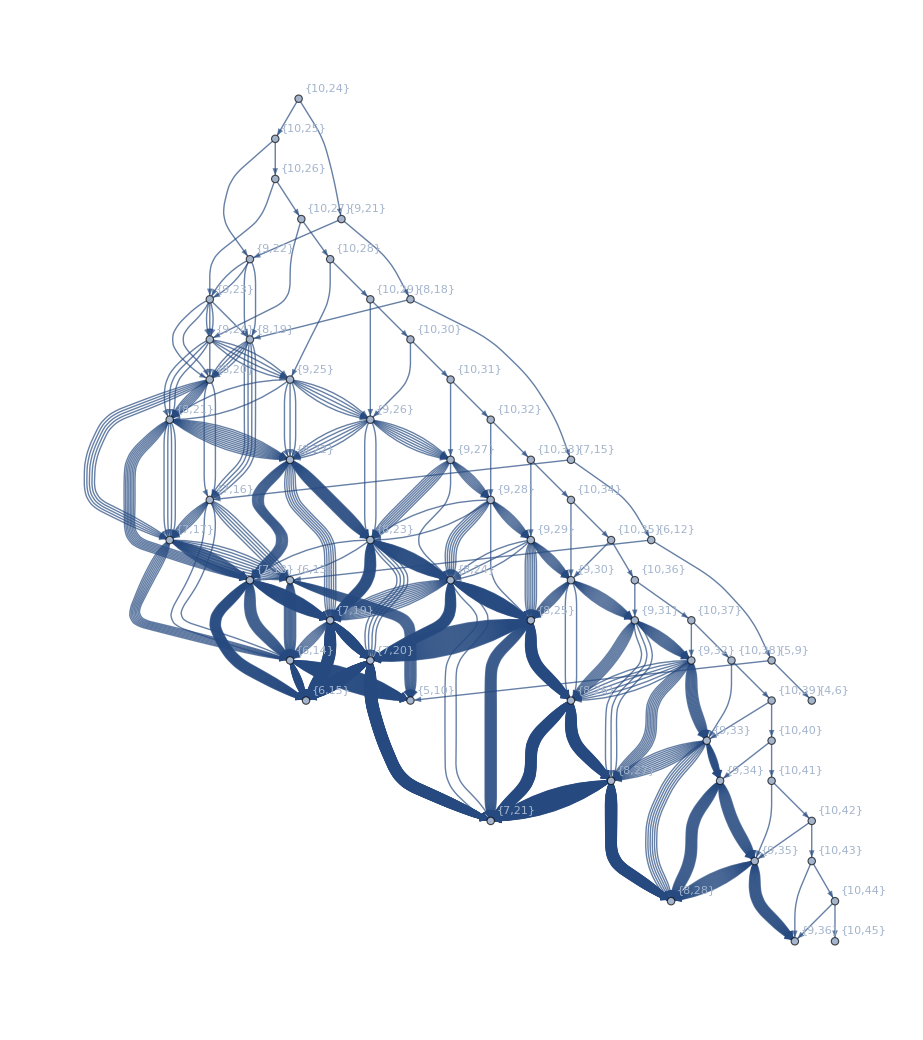

```mathematica
gg2=Graph[FindFormulaPath[MinimalGraph[9]],VertexLabels->"Name",GraphLayout->"LayeredDigraphDrawing"]
```

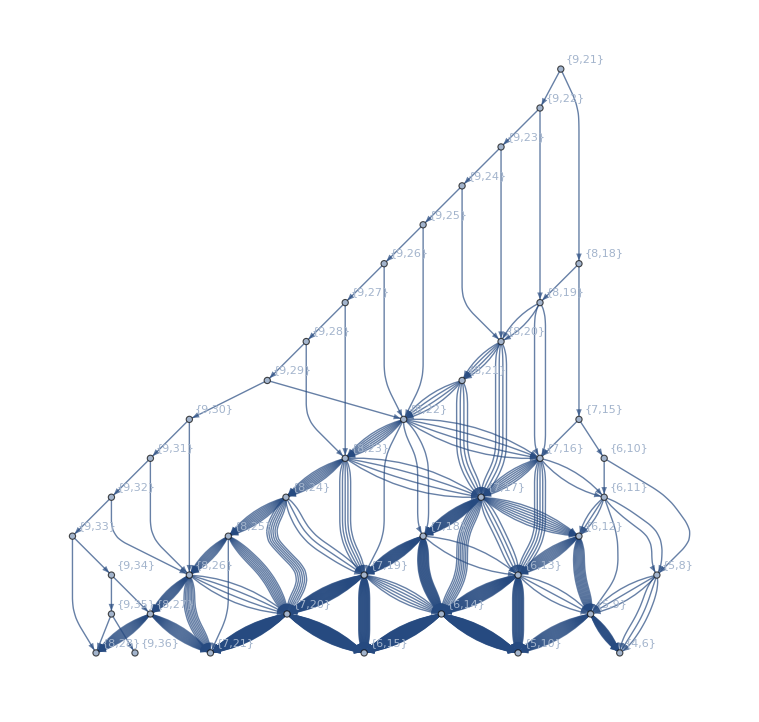

```mathematica
gg2=Graph[FindFormulaPath[JacobsThalGraph2[9]],VertexLabels->"Name",GraphLayout->"LayeredDigraphDrawing"]
```

```mathematica
Table[v->VertexInDegree[gg2,v],{v,Select[VertexList[gg2],VertexOutDegree[gg2,#]==0&]}]
```

{{8,28}→15,{9,36}→1,{7,21}→70,{6,15}→126,{5,10}→91,{4,6}→21}

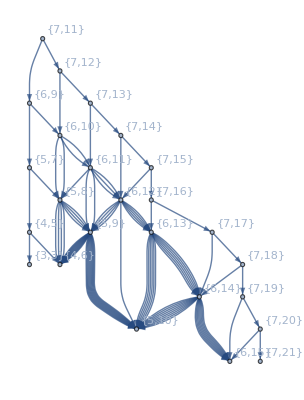

```mathematica
gg2=Graph[FindFormulaPath[LadderGraph[7]],VertexLabels->"Name",GraphLayout->"LayeredDigraphDrawing"]
```

```mathematica
Table[v->VertexInDegree[gg2,v],{v,Select[VertexList[gg2],VertexOutDegree[gg2,#]==0&]}]
```

{{6,15}→10,{7,21}→1,{5,10}→25,{4,6}→15,{3,3}→1}